```mathematica
Define a function that generates random walks (p_{t+1} = p_t + e_t ).
```

```mathematica
RandomWalk[n_]:=
Module[{rv,s},
rv=Table[If[Random[Real, {-1, 1}] < 0, -20, 20], {n}];
s={0};
Label[start];
  s=Join[s,{s[[-1]]+rv[[Length[s]]]}];
  If[Length[s]<n,Goto[start]];
Return[s]]
```

```mathematica
Generate a random walk 'R'.
```

```mathematica
R = RandomWalk[100];
```

```mathematica
rangeR = {Min[R], Max[R]}
```

{-200,120}

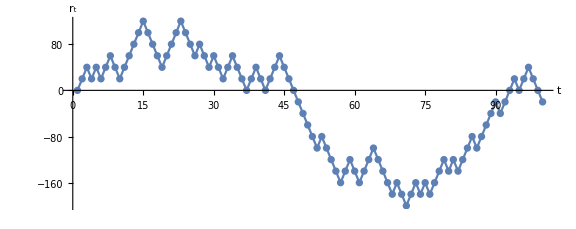

```mathematica
Show[ListPlot[R, PlotRange -> {{0, 100.2}, rangeR}, AxesLabel -> {"t", Subscript["r", "t"]}, LabelStyle->Directive[Medium], AspectRatio -> 0.4, ImageSize -> Large], ListPlot[R, PlotRange -> {{0, 100}, rangeR}, Joined -> True]]
```

```mathematica
Generate a random walk 'S'.
```

```mathematica
S = RandomWalk[100];
```

```mathematica
rangeS = {Min[S], Max[S]}
```

{-120,100}

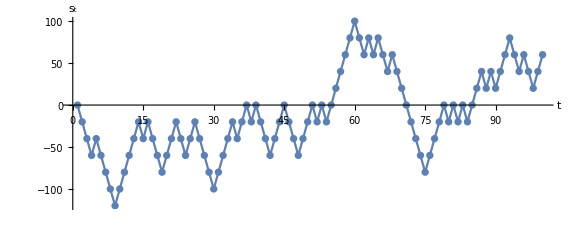

```mathematica
Show[ListPlot[S, PlotRange -> {{0, 100.2}, rangeS}, AxesLabel -> {"t", Subscript["s", "t"]}, LabelStyle->Directive[Medium], AspectRatio -> 0.4, ImageSize -> Large], ListPlot[S, PlotRange -> {{0, 100}, rangeS}, Joined -> True](*,Graphics[{Dashing[{0.005, 0.005, 0.005}], Line[{{0, -40}, {5, -40}, {5, 0}}]}],Graphics[{Dashing[{0.005, 0.005, 0.005}], Line[{{0, 260}, {90, 260}, {90, 0}}]}]*)]
```

```mathematica
Plot  pairs of values from 'R' and 'S'.
```

```mathematica
Transpose[{R, S}]
```

{{0,0},{20,-20},{0,-40},{20,-60},{40,-40},{20,-60},{0,-80},{20,-100},{0,-120},{-20,-100},{-40,-80},{-20,-60},{-40,-40},{-20,-20},{-40,-40},{-60,-20},{-40,-40},{-20,-60},{0,-80},{-20,-60},{-40,-40},{-60,-20},{-80,-40},{-60,-60},{-40,-40},{-60,-20},{-80,-40},{-60,-60},{-80,-80},{-100,-100},{-80,-80},{-100,-60},{-80,-40},{-60,-20},{-40,-40},{-60,-20},{-80,0},{-100,-20},{-80,0},{-100,-20},{-80,-40},{-100,-60},{-120,-40},{-140,-20},{-160,0},{-180,-20},{-160,-40},{-140,-60},{-120,-40},{-100,-20},{-120,0},{-140,-20},{-160,0},{-140,-20},{-120,0},{-100,20},{-80,40},{-60,60},{-40,80},{-60,100},{-40,80},{-60,60},{-80,80},{-60,60},{-80,80},{-100,60},{-120,40},{-100,60},{-80,40},{-60,20},{-40,0},{-20,-20},{-40,-40},{-20,-60},{-40,-80},{-20,-60},{0,-40},{-20,-20},{0,0},{-20,-20},{0,0},{20,-20},{40,0},{60,-20},{40,0},{20,20},{40,40},{60,20},{40,40},{20,20},{40,40},{20,60},{40,80},{20,60},{40,40},{20,60},{40,40},{20,20},{40,40},{20,60}}

```mathematica
Regress values of  'S' onto values of 'R'.
```

```mathematica
r = LinearModelFit[Transpose[{R, S}], {x}, x]
```

FittedModel[-7.73628+0.0894379 x]

```mathematica
Display the coefficients from the regression and the p-values.
```

```mathematica
r["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -7.73628 | 6.12452 | -1.26317 | 0.209527
x | 0.0894379 | 0.0848665 | 1.05387 | 0.294536